```mathematica
l="30";
```

```mathematica
For[dd=0.0816,dd<0.089,dd+=0.001,
d=ToString[dd];
Print[dd];
ddcb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/DDCB-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ClearAll[a,b];
ddcb1=ddcb[[All,1]];
ddcb2=ddcb[[All,2]];
data2=Table[{ddcb1[[i]],Log[ddcb2[[i]]]},{i,1,Length[ddcb1]}];
For[n=100,n<500,n+=25,
data=Table[ddcb[[i]],{i,4,n}];
model=a*Exp[-r/ζ]*r^b;
nlf=NonlinearModelFit[data,model,{a,ζ,b},r];
val=nlf["ParameterTableEntries"];
Print[val[[1]][[1]],"  ",val[[2]][[1]],"  ",val[[3]][[1]],"  "]
]
]
```

```mathematica
a5k[dd][n]=val[[1]][[1]];
z5k[dd][n]=val[[2]][[1]];
b5k[dd][n]=val[[3]][[1]];
```

```mathematica
a5k[0.088][100]
z5k[0.086][125]
b5k[0.086][100]
```

a5k[0.088][100]

z5k[0.086][125]

b5k[0.086][100]

{(0.220485 ⅇ^(-0.025636 r))/r^0.382145, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.220485 | 0.013521 | 16.3068 | 1.73743×10^-14
ζ | 39.0077 | 8.10695 | 4.81164 | 0.0000670443
b | -0.382145 | 0.0525841 | -7.2673 | 1.65434×10^-7}

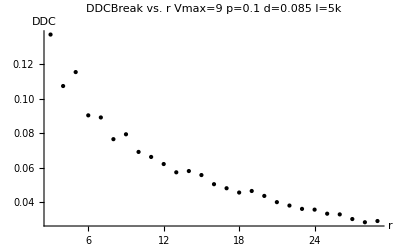

```mathematica
v="9";
d="0.085";
l="5";

n=30;
ddcb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/DDCB-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ClearAll[a,b];
ddcb1=ddcb[[All,1]];
ddcb2=ddcb[[All,2]];
data=Table[ddcb[[i]],{i,4,n}];
data2=Table[{ddcb1[[i]],Log[ddcb2[[i]]]},{i,4,n}];

model=a*Exp[-r/ζ]*r^b;


nlf=NonlinearModelFit[data,model,{a,ζ,b},r];

nlf[{"BestFit","ParameterTable"}]

Print[val[[1]][[1]],"  ",val[[2]][[1]],"  ",val[[3]][[1]],"  "]
Plot[{modelf1[r]},{r,1,n},PlotLabel->"DDCBreak vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",Epilog->Map[Point,{data}],AxesLabel->{r,DDC},PlotRange->{Full,{2,1.2*ddcb2[[4]]}}]
```

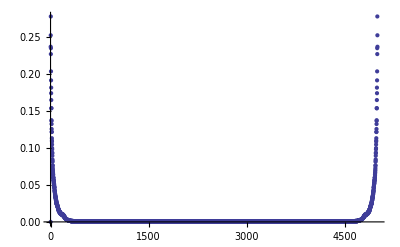

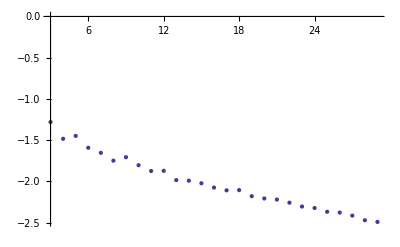

```mathematica
ListPlot[ddcb2,PlotRange->Full]
ListPlot[data2,PlotRange->Full]
```

```mathematica
model2=Log[a]-r/ζ+b*Log[r];
nlf2=NonlinearModelFit[data2,model2,{a,ζ,b},r];
nlf2[{"BestFit","ParameterTable"}]
Plot[{modelf2[r]},{r,1,n},PlotLabel->"DDCBreak vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",Epilog->Map[Point,{data}],AxesLabel->{r,DDC},PlotRange->{Full,{2,1.2*Log[ddcb2[[4]]]}}]
```